# MGDrivE: Yorkeys Knob Analysis

## 0) Functions

```mathematica
<<colorBlender`
SetDirectory[NotebookDirectory[]];
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->17.5,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
AxesLabel->(Style[#,40]&/@{"Time","Genotype Breakdown"}),
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## 1) Calculate Fit (Fixation)

```mathematica
{timeRange,day}={{1,999},999};
flattenedData=Import["./50TX.csv"];
```

```mathematica
rawGrid=Flatten[{
Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}],
Transpose[
{
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]
},1];
```

```mathematica
boundary=Table[
slice=Cases[rawGrid,{a_,i,c_}->{a,i,c}]//Sort;
inflection=Cases[slice,{a_,b_,c_}/;c>.5];
If[inflection≠{},
inflection[[1,1;;2]],
Unevaluated[Sequence[]]
]
,{i,rawGrid[[All,2]]//DeleteDuplicates}]//Sort;
points=ListPlot[boundary,PlotStyle->White];
nlm=NonlinearModelFit[boundary,a+ⅇ^(-(c+b*x)),{a,b,c},x]//Quiet
fitPlot=Plot[nlm[x],{x,0,50},AspectRatio->1,PlotRange->{{0,20},{0,2}},PlotStyle->Directive[White,Opacity[.5],Thickness[.035]]];
```

FittedModel[0.243193+ⅇ^(0.716423-0.215391 x)]

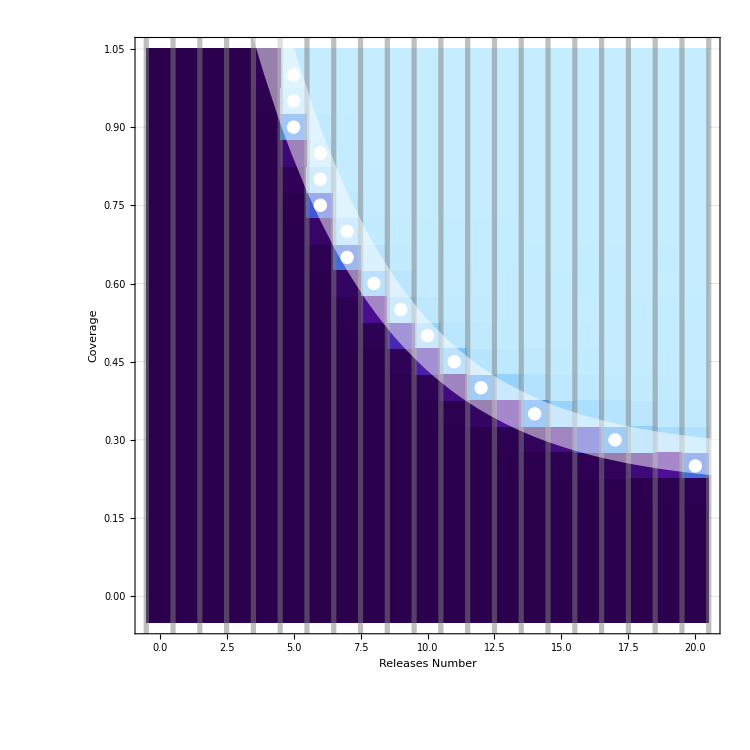

```mathematica
density=ListDensityPlot[
rawGrid
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->750
,InterpolationOrder->0
,FrameLabel->(Style[#,50]&/@{"Releases Number","Coverage","Day: "<>StringPadLeft[ToString[day],3]})
,FrameTicksStyle->Directive[25]
,PlotRange->{{-.5,20.5},{-.05,1.05}}
,PlotRangePadding->0
];
Show[density,points,fitPlot]
```

## 2) Calculate Fit (Remediation)

```mathematica
{timeRange,day}={{1,999},999};
flattenedData=Import["./50TR.csv"];
```

```mathematica
rawGrid=Flatten[{
Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}],
Transpose[
{
ConstantArray[0,flattenedData[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[1,flattenedData[[All,2]]//DeleteDuplicates//Length]
}]
},1];
```

```mathematica
boundary=Table[
slice=Cases[rawGrid,{a_,i,c_}->{a,i,c}]//Sort;
inflection=Cases[slice,{a_,b_,c_}/;c<.5];
If[inflection≠{},
inflection[[1,1;;2]],
Unevaluated[Sequence[]]
]
,{i,rawGrid[[All,2]]//DeleteDuplicates}]//Sort;
points=ListPlot[boundary,PlotStyle->White];
nlm=NonlinearModelFit[boundary,a+ⅇ^(-(c+b*x)),{a,b,c},x]//Quiet
fitPlot=Plot[nlm[x],{x,0,50},AspectRatio->1,PlotRange->{{0,20},{0,2}},PlotStyle->Directive[White,Opacity[.5],Thickness[.03]]];
```

FittedModel[0.226235+ⅇ^(0.657184-0.198491 x)]

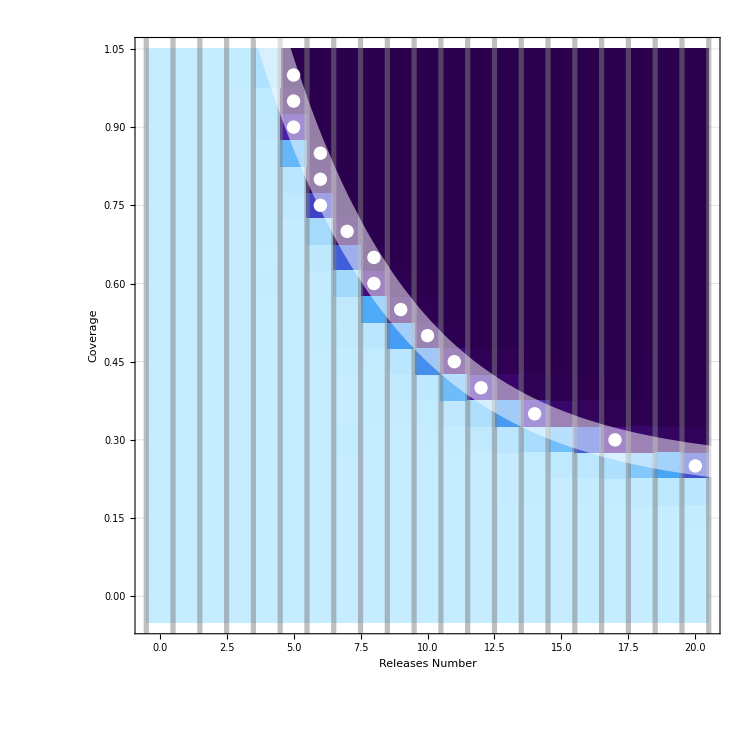

```mathematica
density=ListDensityPlot[
rawGrid
,ColorFunction->ColorData[{"DeepSeaColors",{0,1}}]
,ColorFunctionScaling->False
,GridLines->{Range[-.5,20.5,1],Range[-1.025,1.05,.05]}
,GridLinesStyle->Directive[Gray,Thickness[.005],Opacity[.5]]
,ImageSize->750
,InterpolationOrder->0
,FrameLabel->(Style[#,50]&/@{"Releases Number","Coverage","Day: "<>StringPadLeft[ToString[day],3]})
,FrameTicksStyle->Directive[25]
,PlotRange->{{-.5,20.5},{-.05,1.05}}
,PlotRangePadding->0
];
Show[density,points,fitPlot]
```

## Comparison

Static

```mathematica
nlm//Normal
```

0.243193+ⅇ^(0.716423-0.215391 x)

```mathematica
nlm//Normal
```

0.226235+ⅇ^(0.657184-0.198491 x)

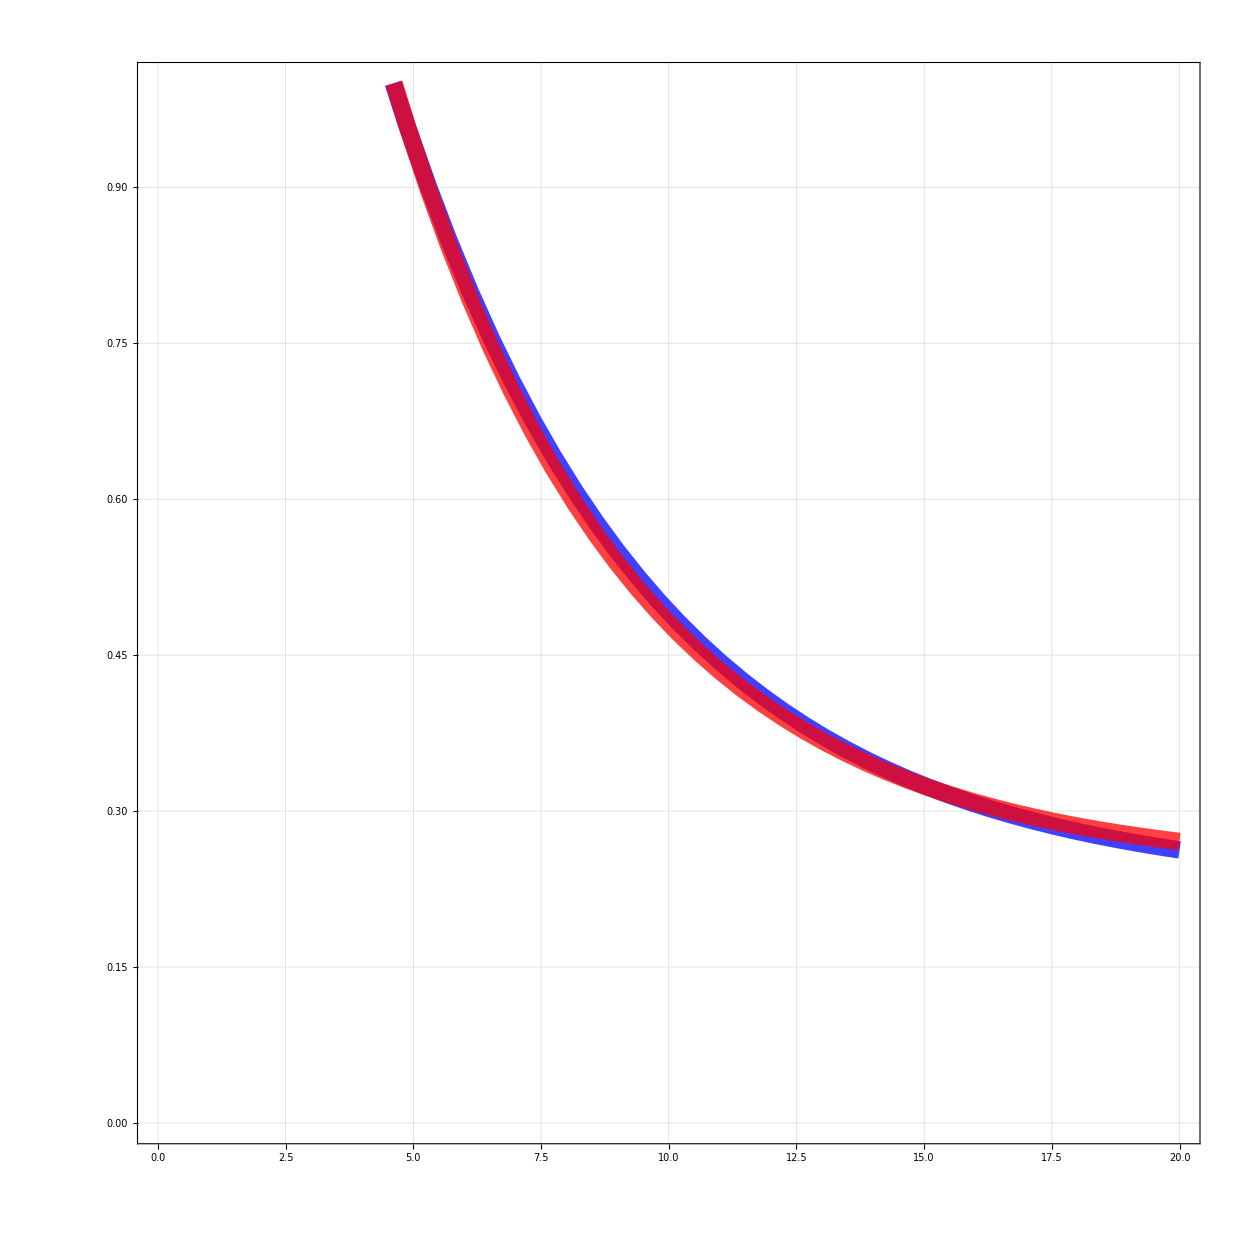

```mathematica
Plot[{0.22623548185277856+ⅇ^(0.6571841511168854-0.19849061959865164 x),0.24319341741932418+ⅇ^(0.7164231046548308-0.21539137726449753 x)}
,{x,0,20}
,AspectRatio->1
,Frame->True
,FrameStyle->Thick
,FrameTicksStyle->20
,GridLines->Automatic
,ImageSize->1250
,PlotRange->{0,1}
,PlotStyle->{Directive[Thickness[.01],Opacity[.75],Blue],Directive[Thickness[.01],Opacity[.75],Red]}
]
```

Difference

```mathematica
{timeRange,day}={{1,999},999};
flattenedDataTX=Import["./50TX.csv"];
flattenedDataTR=Import["./50TR.csv"];
```

```mathematica
{gridTX,gridTR}=Flatten[{
Cases[flattenedData,{a_,b_,day,c_}->{a,b,c}],
Transpose[
{
ConstantArray[0,#[[All,2]]//DeleteDuplicates//Length],
flattenedData[[All,2]]//DeleteDuplicates,
ConstantArray[0,#[[All,2]]//DeleteDuplicates//Length]
}]
},1]&/@{flattenedDataTX,flattenedDataTR};
```

```mathematica
Sort[gridTX]
Sort[gridTR]
```

{{0,0.,0},{0,0.05,0},{0,0.1,0},{0,0.15,0},{0,0.2,0},{0,0.25,0},{0,0.3,0},{0,0.35,0},{0,0.4,0},{0,0.45,0},{0,0.5,0},{0,0.55,0},{0,0.6,0},{0,0.65,0},{0,0.7,0},{0,0.75,0},{0,0.8,0},{0,0.85,0},{0,0.9,0},{0,0.95,0},{0,1.,0},{1,0.,1.},{1,0.05,1.},{1,0.1,1.},{1,0.15,1.},{1,0.2,1.},{1,0.25,1.},{1,0.3,1.},{1,0.35,1.},{1,0.4,0.999978},{1,0.45,1.},{1,0.5,0.999927},{1,0.55,0.999977},{1,0.6,0.999962},{1,0.65,0.999946},{1,0.7,0.999958},{1,0.75,0.999997},{1,0.8,0.999995},{1,0.85,0.999961},{1,0.9,0.999976},{1,0.95,0.999957},{1,1.,0.999999},{2,0.,1.},{2,0.05,1.},{2,0.1,1.},{2,0.15,1.},{2,0.2,0.999895},{2,0.25,0.999936},{2,0.3,0.999997},{2,0.35,0.999927},{2,0.4,0.999992},{2,0.45,0.99988},{2,0.5,0.999982},{2,0.55,0.999814},{2,0.6,0.999851},{2,0.65,0.999953},{2,0.7,0.999832},{2,0.75,0.999852},{2,0.8,0.999888},{2,0.85,0.999671},{2,0.9,0.999797},{2,0.95,0.999755},{2,1.,0.999662},{3,0.,1.},{3,0.05,0.99997},{3,0.1,1.},{3,0.15,0.999851},{3,0.2,0.999933},{3,0.25,0.999949},{3,0.3,0.999826},{3,0.35,0.999761},{3,0.4,0.999922},{3,0.45,0.999964},{3,0.5,0.999883},{3,0.55,0.999803},{3,0.6,0.999728},{3,0.65,0.999692},{3,0.7,0.999825},{3,0.75,0.999512},{3,0.8,0.999465},{3,0.85,0.999749},{3,0.9,0.999595},{3,0.95,0.999445},{3,1.,0.999168},{4,0.,1.},{4,0.05,0.999999},{4,0.1,1.},{4,0.15,0.999907},{4,0.2,0.999919},{4,0.25,0.999892},{4,0.3,0.999727},{4,0.35,0.999745},{4,0.4,0.999844},{4,0.45,0.999647},{4,0.5,0.999554},{4,0.55,0.999679},{4,0.6,0.99917},{4,0.65,0.999388},{4,0.7,0.99924},{4,0.75,0.999121},{4,0.8,0.998993},{4,0.85,0.998439},{4,0.9,0.994257},{4,0.95,0.988052},{4,1.,0.958519},{5,0.,1.},{5,0.05,1.},{5,0.1,0.999875},{5,0.15,0.99979},{5,0.2,0.999702},{5,0.25,0.999707},{5,0.3,0.999634},{5,0.35,0.999784},{5,0.4,0.999802},{5,0.45,0.999618},{5,0.5,0.999452},{5,0.55,0.999225},{5,0.6,0.999184},{5,0.65,0.998895},{5,0.7,0.997279},{5,0.75,0.989867},{5,0.8,0.976778},{5,0.85,0.807842},{5,0.9,0.301686},{5,0.95,0.042375},{5,1.,0.00881822},{6,0.,1.},{6,0.05,1.},{6,0.1,0.999975},{6,0.15,0.999812},{6,0.2,0.999627},{6,0.25,0.999656},{6,0.3,0.999549},{6,0.35,0.999525},{6,0.4,0.99946},{6,0.45,0.999277},{6,0.5,0.999099},{6,0.55,0.997031},{6,0.6,0.996975},{6,0.65,0.98491},{6,0.7,0.93526},{6,0.75,0.440231},{6,0.8,0.050541},{6,0.85,0.014298},{6,0.9,0.00358713},{6,0.95,0.000946364},{6,1.,0.000328047},{7,0.,1.},{7,0.05,1.},{7,0.1,0.999844},{7,0.15,0.99987},{7,0.2,0.999707},{7,0.25,0.999876},{7,0.3,0.999246},{7,0.35,0.999792},{7,0.4,0.999319},{7,0.45,0.998966},{7,0.5,0.994521},{7,0.55,0.989402},{7,0.6,0.930225},{7,0.65,0.535001},{7,0.7,0.0617678},{7,0.75,0.011611},{7,0.8,0.00356742},{7,0.85,0.000849216},{7,0.9,0.000374797},{7,0.95,0.000693296},{7,1.,0.000245138},{8,0.,1.},{8,0.05,0.999907},{8,0.1,0.999902},{8,0.15,0.999857},{8,0.2,0.999828},{8,0.25,0.999677},{8,0.3,0.999388},{8,0.35,0.999026},{8,0.4,0.998977},{8,0.45,0.996066},{8,0.5,0.978099},{8,0.55,0.759644},{8,0.6,0.170242},{8,0.65,0.0232204},{8,0.7,0.00371494},{8,0.75,0.00215963},{8,0.8,0.000949467},{8,0.85,0.000727454},{8,0.9,0.000144129},{8,0.95,0.00050867},{8,1.,0.0000544328},{9,0.,1.},{9,0.05,0.999933},{9,0.1,0.999813},{9,0.15,0.99964},{9,0.2,0.999812},{9,0.25,0.999504},{9,0.3,0.999505},{9,0.35,0.998492},{9,0.4,0.993973},{9,0.45,0.976494},{9,0.5,0.715153},{9,0.55,0.0870292},{9,0.6,0.0142544},{9,0.65,0.00521887},{9,0.7,0.00159589},{9,0.75,0.000749344},{9,0.8,0.000490148},{9,0.85,0.000505588},{9,0.9,0.000536146},{9,0.95,0.000204654},{9,1.,1.45355×10^-6},{10,0.,1.},{10,0.05,0.999904},{10,0.1,0.999751},{10,0.15,0.999505},{10,0.2,0.999748},{10,0.25,0.999421},{10,0.3,0.99888},{10,0.35,0.997162},{10,0.4,0.985628},{10,0.45,0.673743},{10,0.5,0.0772518},{10,0.55,0.0200326},{10,0.6,0.00721752},{10,0.65,0.00212421},{10,0.7,0.000936357},{10,0.75,0.000884406},{10,0.8,0.000615816},{10,0.85,0.000352622},{10,0.9,0.000232468},{10,0.95,0.000129726},{10,1.,0.},{11,0.,1.},{11,0.05,0.99988},{11,0.1,0.999888},{11,0.15,0.999671},{11,0.2,0.999565},{11,0.25,0.999633},{11,0.3,0.997324},{11,0.35,0.987647},{11,0.4,0.825707},{11,0.45,0.145218},{11,0.5,0.0171189},{11,0.55,0.00462831},{11,0.6,0.000947729},{11,0.65,0.000364154},{11,0.7,0.000649406},{11,0.75,0.000746429},{11,0.8,0.000390025},{11,0.85,0.000195076},{11,0.9,0.000308998},{11,0.95,0.0000828939},{11,1.,0.},{12,0.,1.},{12,0.05,0.999717},{12,0.1,0.999831},{12,0.15,0.999706},{12,0.2,0.999376},{12,0.25,0.999301},{12,0.3,0.990519},{12,0.35,0.953646},{12,0.4,0.298207},{12,0.45,0.0319716},{12,0.5,0.00783568},{12,0.55,0.00232863},{12,0.6,0.00129582},{12,0.65,0.000977906},{12,0.7,0.000569005},{12,0.75,0.000509477},{12,0.8,0.000273169},{12,0.85,0.000485717},{12,0.9,0.000321938},{12,0.95,0.000184153},{12,1.,0.},{13,0.,1.},{13,0.05,0.999857},{13,0.1,0.999861},{13,0.15,0.999807},{13,0.2,0.998757},{13,0.25,0.997492},{13,0.3,0.979631},{13,0.35,0.705611},{13,0.4,0.0949242},{13,0.45,0.0202876},{13,0.5,0.00425496},{13,0.55,0.00194875},{13,0.6,0.000853347},{13,0.65,0.00109983},{13,0.7,0.000784833},{13,0.75,0.000589682},{13,0.8,0.000458847},{13,0.85,0.000584104},{13,0.9,0.00012699},{13,0.95,0.000153593},{13,1.,0.},{14,0.,1.},{14,0.05,0.999925},{14,0.1,0.999887},{14,0.15,0.999444},{14,0.2,0.999135},{14,0.25,0.997003},{14,0.3,0.945772},{14,0.35,0.333112},{14,0.4,0.0256023},{14,0.45,0.00697842},{14,0.5,0.00307183},{14,0.55,0.000869343},{14,0.6,0.00090532},{14,0.65,0.000455224},{14,0.7,0.00069414},{14,0.75,0.000525375},{14,0.8,0.000297697},{14,0.85,0.000128443},{14,0.9,0.000237477},{14,0.95,0.},{14,1.,0.},{15,0.,1.},{15,0.05,0.999839},{15,0.1,0.999937},{15,0.15,0.999653},{15,0.2,0.999547},{15,0.25,0.988076},{15,0.3,0.832437},{15,0.35,0.101202},{15,0.4,0.0177178},{15,0.45,0.00734158},{15,0.5,0.00225906},{15,0.55,0.000633461},{15,0.6,0.000786109},{15,0.65,0.000756041},{15,0.7,0.000418967},{15,0.75,0.000623897},{15,0.8,0.000279365},{15,0.85,0.000189486},{15,0.9,0.000189118},{15,0.95,0.000172712},{15,1.,0.},{16,0.,1.},{16,0.05,0.999964},{16,0.1,0.99993},{16,0.15,0.999307},{16,0.2,0.99916},{16,0.25,0.982842},{16,0.3,0.519317},{16,0.35,0.0566511},{16,0.4,0.0061165},{16,0.45,0.00245314},{16,0.5,0.000830747},{16,0.55,0.00098167},{16,0.6,0.000933007},{16,0.65,0.000785687},{16,0.7,0.000672493},{16,0.75,0.000471239},{16,0.8,0.000297948},{16,0.85,0.000220185},{16,0.9,0.000181808},{16,0.95,0.000184326},{16,1.,0.},{17,0.,1.},{17,0.05,1.},{17,0.1,0.999808},{17,0.15,0.999616},{17,0.2,0.996379},{17,0.25,0.95548},{17,0.3,0.213222},{17,0.35,0.0210826},{17,0.4,0.00515566},{17,0.45,0.0032514},{17,0.5,0.00133405},{17,0.55,0.000501454},{17,0.6,0.000820949},{17,0.65,0.000792308},{17,0.7,0.000601269},{17,0.75,0.000441558},{17,0.8,0.000333066},{17,0.85,0.000214906},{17,0.9,0.000256446},{17,0.95,0.0000877705},{17,1.,0.},{18,0.,1.},{18,0.05,0.999859},{18,0.1,0.999979},{18,0.15,0.999466},{18,0.2,0.994023},{18,0.25,0.867384},{18,0.3,0.100875},{18,0.35,0.0148492},{18,0.4,0.00240319},{18,0.45,0.00195525},{18,0.5,0.00119209},{18,0.55,0.00116814},{18,0.6,0.000818944},{18,0.65,0.000227486},{18,0.7,0.000410865},{18,0.75,0.000405078},{18,0.8,0.000191465},{18,0.85,0.000127801},{18,0.9,0.000203424},{18,0.95,0.000210007},{18,1.,0.},{19,0.,1.},{19,0.05,0.999821},{19,0.1,0.999524},{19,0.15,0.999524},{19,0.2,0.984634},{19,0.25,0.742666},{19,0.3,0.0617172},{19,0.35,0.00827835},{19,0.4,0.0025745},{19,0.45,0.00280484},{19,0.5,0.00076387},{19,0.55,0.00129254},{19,0.6,0.000773441},{19,0.65,0.000341252},{19,0.7,0.000313447},{19,0.75,0.000200974},{19,0.8,0.000319985},{19,0.85,0.000291704},{19,0.9,0.000100657},{19,0.95,0.000142097},{19,1.,0.},{20,0.,1.},{20,0.05,0.999695},{20,0.1,0.99974},{20,0.15,0.999103},{20,0.2,0.975314},{20,0.25,0.489939},{20,0.3,0.0384356},{20,0.35,0.00806807},{20,0.4,0.0031482},{20,0.45,0.00129568},{20,0.5,0.000996193},{20,0.55,0.00101364},{20,0.6,0.000525822},{20,0.65,0.000558823},{20,0.7,0.000302775},{20,0.75,0.000318246},{20,0.8,0.000287483},{20,0.85,0.000131314},{20,0.9,0.000271789},{20,0.95,0.},{20,1.,0.}}

{{0,0.,0},{0,0.05,0},{0,0.1,0},{0,0.15,0},{0,0.2,0},{0,0.25,0},{0,0.3,0},{0,0.35,0},{0,0.4,0},{0,0.45,0},{0,0.5,0},{0,0.55,0},{0,0.6,0},{0,0.65,0},{0,0.7,0},{0,0.75,0},{0,0.8,0},{0,0.85,0},{0,0.9,0},{0,0.95,0},{0,1.,0},{1,0.,1.},{1,0.05,1.},{1,0.1,1.},{1,0.15,1.},{1,0.2,1.},{1,0.25,1.},{1,0.3,1.},{1,0.35,1.},{1,0.4,0.999978},{1,0.45,1.},{1,0.5,0.999927},{1,0.55,0.999977},{1,0.6,0.999962},{1,0.65,0.999946},{1,0.7,0.999958},{1,0.75,0.999997},{1,0.8,0.999995},{1,0.85,0.999961},{1,0.9,0.999976},{1,0.95,0.999957},{1,1.,0.999999},{2,0.,1.},{2,0.05,1.},{2,0.1,1.},{2,0.15,1.},{2,0.2,0.999895},{2,0.25,0.999936},{2,0.3,0.999997},{2,0.35,0.999927},{2,0.4,0.999992},{2,0.45,0.99988},{2,0.5,0.999982},{2,0.55,0.999814},{2,0.6,0.999851},{2,0.65,0.999953},{2,0.7,0.999832},{2,0.75,0.999852},{2,0.8,0.999888},{2,0.85,0.999671},{2,0.9,0.999797},{2,0.95,0.999755},{2,1.,0.999662},{3,0.,1.},{3,0.05,0.99997},{3,0.1,1.},{3,0.15,0.999851},{3,0.2,0.999933},{3,0.25,0.999949},{3,0.3,0.999826},{3,0.35,0.999761},{3,0.4,0.999922},{3,0.45,0.999964},{3,0.5,0.999883},{3,0.55,0.999803},{3,0.6,0.999728},{3,0.65,0.999692},{3,0.7,0.999825},{3,0.75,0.999512},{3,0.8,0.999465},{3,0.85,0.999749},{3,0.9,0.999595},{3,0.95,0.999445},{3,1.,0.999168},{4,0.,1.},{4,0.05,0.999999},{4,0.1,1.},{4,0.15,0.999907},{4,0.2,0.999919},{4,0.25,0.999892},{4,0.3,0.999727},{4,0.35,0.999745},{4,0.4,0.999844},{4,0.45,0.999647},{4,0.5,0.999554},{4,0.55,0.999679},{4,0.6,0.99917},{4,0.65,0.999388},{4,0.7,0.99924},{4,0.75,0.999121},{4,0.8,0.998993},{4,0.85,0.998439},{4,0.9,0.994257},{4,0.95,0.988052},{4,1.,0.958519},{5,0.,1.},{5,0.05,1.},{5,0.1,0.999875},{5,0.15,0.99979},{5,0.2,0.999702},{5,0.25,0.999707},{5,0.3,0.999634},{5,0.35,0.999784},{5,0.4,0.999802},{5,0.45,0.999618},{5,0.5,0.999452},{5,0.55,0.999225},{5,0.6,0.999184},{5,0.65,0.998895},{5,0.7,0.997279},{5,0.75,0.989867},{5,0.8,0.976778},{5,0.85,0.807842},{5,0.9,0.301686},{5,0.95,0.042375},{5,1.,0.00881822},{6,0.,1.},{6,0.05,1.},{6,0.1,0.999975},{6,0.15,0.999812},{6,0.2,0.999627},{6,0.25,0.999656},{6,0.3,0.999549},{6,0.35,0.999525},{6,0.4,0.99946},{6,0.45,0.999277},{6,0.5,0.999099},{6,0.55,0.997031},{6,0.6,0.996975},{6,0.65,0.98491},{6,0.7,0.93526},{6,0.75,0.440231},{6,0.8,0.050541},{6,0.85,0.014298},{6,0.9,0.00358713},{6,0.95,0.000946364},{6,1.,0.000328047},{7,0.,1.},{7,0.05,1.},{7,0.1,0.999844},{7,0.15,0.99987},{7,0.2,0.999707},{7,0.25,0.999876},{7,0.3,0.999246},{7,0.35,0.999792},{7,0.4,0.999319},{7,0.45,0.998966},{7,0.5,0.994521},{7,0.55,0.989402},{7,0.6,0.930225},{7,0.65,0.535001},{7,0.7,0.0617678},{7,0.75,0.011611},{7,0.8,0.00356742},{7,0.85,0.000849216},{7,0.9,0.000374797},{7,0.95,0.000693296},{7,1.,0.000245138},{8,0.,1.},{8,0.05,0.999907},{8,0.1,0.999902},{8,0.15,0.999857},{8,0.2,0.999828},{8,0.25,0.999677},{8,0.3,0.999388},{8,0.35,0.999026},{8,0.4,0.998977},{8,0.45,0.996066},{8,0.5,0.978099},{8,0.55,0.759644},{8,0.6,0.170242},{8,0.65,0.0232204},{8,0.7,0.00371494},{8,0.75,0.00215963},{8,0.8,0.000949467},{8,0.85,0.000727454},{8,0.9,0.000144129},{8,0.95,0.00050867},{8,1.,0.0000544328},{9,0.,1.},{9,0.05,0.999933},{9,0.1,0.999813},{9,0.15,0.99964},{9,0.2,0.999812},{9,0.25,0.999504},{9,0.3,0.999505},{9,0.35,0.998492},{9,0.4,0.993973},{9,0.45,0.976494},{9,0.5,0.715153},{9,0.55,0.0870292},{9,0.6,0.0142544},{9,0.65,0.00521887},{9,0.7,0.00159589},{9,0.75,0.000749344},{9,0.8,0.000490148},{9,0.85,0.000505588},{9,0.9,0.000536146},{9,0.95,0.000204654},{9,1.,1.45355×10^-6},{10,0.,1.},{10,0.05,0.999904},{10,0.1,0.999751},{10,0.15,0.999505},{10,0.2,0.999748},{10,0.25,0.999421},{10,0.3,0.99888},{10,0.35,0.997162},{10,0.4,0.985628},{10,0.45,0.673743},{10,0.5,0.0772518},{10,0.55,0.0200326},{10,0.6,0.00721752},{10,0.65,0.00212421},{10,0.7,0.000936357},{10,0.75,0.000884406},{10,0.8,0.000615816},{10,0.85,0.000352622},{10,0.9,0.000232468},{10,0.95,0.000129726},{10,1.,0.},{11,0.,1.},{11,0.05,0.99988},{11,0.1,0.999888},{11,0.15,0.999671},{11,0.2,0.999565},{11,0.25,0.999633},{11,0.3,0.997324},{11,0.35,0.987647},{11,0.4,0.825707},{11,0.45,0.145218},{11,0.5,0.0171189},{11,0.55,0.00462831},{11,0.6,0.000947729},{11,0.65,0.000364154},{11,0.7,0.000649406},{11,0.75,0.000746429},{11,0.8,0.000390025},{11,0.85,0.000195076},{11,0.9,0.000308998},{11,0.95,0.0000828939},{11,1.,0.},{12,0.,1.},{12,0.05,0.999717},{12,0.1,0.999831},{12,0.15,0.999706},{12,0.2,0.999376},{12,0.25,0.999301},{12,0.3,0.990519},{12,0.35,0.953646},{12,0.4,0.298207},{12,0.45,0.0319716},{12,0.5,0.00783568},{12,0.55,0.00232863},{12,0.6,0.00129582},{12,0.65,0.000977906},{12,0.7,0.000569005},{12,0.75,0.000509477},{12,0.8,0.000273169},{12,0.85,0.000485717},{12,0.9,0.000321938},{12,0.95,0.000184153},{12,1.,0.},{13,0.,1.},{13,0.05,0.999857},{13,0.1,0.999861},{13,0.15,0.999807},{13,0.2,0.998757},{13,0.25,0.997492},{13,0.3,0.979631},{13,0.35,0.705611},{13,0.4,0.0949242},{13,0.45,0.0202876},{13,0.5,0.00425496},{13,0.55,0.00194875},{13,0.6,0.000853347},{13,0.65,0.00109983},{13,0.7,0.000784833},{13,0.75,0.000589682},{13,0.8,0.000458847},{13,0.85,0.000584104},{13,0.9,0.00012699},{13,0.95,0.000153593},{13,1.,0.},{14,0.,1.},{14,0.05,0.999925},{14,0.1,0.999887},{14,0.15,0.999444},{14,0.2,0.999135},{14,0.25,0.997003},{14,0.3,0.945772},{14,0.35,0.333112},{14,0.4,0.0256023},{14,0.45,0.00697842},{14,0.5,0.00307183},{14,0.55,0.000869343},{14,0.6,0.00090532},{14,0.65,0.000455224},{14,0.7,0.00069414},{14,0.75,0.000525375},{14,0.8,0.000297697},{14,0.85,0.000128443},{14,0.9,0.000237477},{14,0.95,0.},{14,1.,0.},{15,0.,1.},{15,0.05,0.999839},{15,0.1,0.999937},{15,0.15,0.999653},{15,0.2,0.999547},{15,0.25,0.988076},{15,0.3,0.832437},{15,0.35,0.101202},{15,0.4,0.0177178},{15,0.45,0.00734158},{15,0.5,0.00225906},{15,0.55,0.000633461},{15,0.6,0.000786109},{15,0.65,0.000756041},{15,0.7,0.000418967},{15,0.75,0.000623897},{15,0.8,0.000279365},{15,0.85,0.000189486},{15,0.9,0.000189118},{15,0.95,0.000172712},{15,1.,0.},{16,0.,1.},{16,0.05,0.999964},{16,0.1,0.99993},{16,0.15,0.999307},{16,0.2,0.99916},{16,0.25,0.982842},{16,0.3,0.519317},{16,0.35,0.0566511},{16,0.4,0.0061165},{16,0.45,0.00245314},{16,0.5,0.000830747},{16,0.55,0.00098167},{16,0.6,0.000933007},{16,0.65,0.000785687},{16,0.7,0.000672493},{16,0.75,0.000471239},{16,0.8,0.000297948},{16,0.85,0.000220185},{16,0.9,0.000181808},{16,0.95,0.000184326},{16,1.,0.},{17,0.,1.},{17,0.05,1.},{17,0.1,0.999808},{17,0.15,0.999616},{17,0.2,0.996379},{17,0.25,0.95548},{17,0.3,0.213222},{17,0.35,0.0210826},{17,0.4,0.00515566},{17,0.45,0.0032514},{17,0.5,0.00133405},{17,0.55,0.000501454},{17,0.6,0.000820949},{17,0.65,0.000792308},{17,0.7,0.000601269},{17,0.75,0.000441558},{17,0.8,0.000333066},{17,0.85,0.000214906},{17,0.9,0.000256446},{17,0.95,0.0000877705},{17,1.,0.},{18,0.,1.},{18,0.05,0.999859},{18,0.1,0.999979},{18,0.15,0.999466},{18,0.2,0.994023},{18,0.25,0.867384},{18,0.3,0.100875},{18,0.35,0.0148492},{18,0.4,0.00240319},{18,0.45,0.00195525},{18,0.5,0.00119209},{18,0.55,0.00116814},{18,0.6,0.000818944},{18,0.65,0.000227486},{18,0.7,0.000410865},{18,0.75,0.000405078},{18,0.8,0.000191465},{18,0.85,0.000127801},{18,0.9,0.000203424},{18,0.95,0.000210007},{18,1.,0.},{19,0.,1.},{19,0.05,0.999821},{19,0.1,0.999524},{19,0.15,0.999524},{19,0.2,0.984634},{19,0.25,0.742666},{19,0.3,0.0617172},{19,0.35,0.00827835},{19,0.4,0.0025745},{19,0.45,0.00280484},{19,0.5,0.00076387},{19,0.55,0.00129254},{19,0.6,0.000773441},{19,0.65,0.000341252},{19,0.7,0.000313447},{19,0.75,0.000200974},{19,0.8,0.000319985},{19,0.85,0.000291704},{19,0.9,0.000100657},{19,0.95,0.000142097},{19,1.,0.},{20,0.,1.},{20,0.05,0.999695},{20,0.1,0.99974},{20,0.15,0.999103},{20,0.2,0.975314},{20,0.25,0.489939},{20,0.3,0.0384356},{20,0.35,0.00806807},{20,0.4,0.0031482},{20,0.45,0.00129568},{20,0.5,0.000996193},{20,0.55,0.00101364},{20,0.6,0.000525822},{20,0.65,0.000558823},{20,0.7,0.000302775},{20,0.75,0.000318246},{20,0.8,0.000287483},{20,0.85,0.000131314},{20,0.9,0.000271789},{20,0.95,0.},{20,1.,0.}}